# Rigid bodies, plastic impact

```mathematica
param={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,mO->3000,r->0.12,γ->0.5};
paramExtraction={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,r->0.12,γ->0.5};
```

```mathematica
θ00=π/2;q10=0;q20=π/3;xb0=4;yb0=2;
```

```mathematica
paramScheme={θ0[t]->θ00,q1[t]->q10,q2[t]->q20,xb[t]->xb0,yb[t]->yb0};
```

## Kinematics

## Manipulator

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | {q1[t],q2[t]}
0 | 0 | 1 | {θ0[t],q1[t],q2[t]}
0 | 0 | 0 | 1)

```mathematica
Mfb=Mrotztrasl[0,{xb[t],yb[t],0}];
```

```mathematica
Mb0=Mrotztrasl[θ0[t],{0,0,0}];
```

```mathematica
Mf0=Mfb.Mb0;Mf0//MatrixForm
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | xb[t]
Sin[θ0[t]] | Cos[θ0[t]] | 0 | yb[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[q1[t],{l1 Cos[q1[t]],l1 Sin[q1[t]],0}];M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | l1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | l1 Sin[q1[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[q2[t],{l2 Cos[q2[t]],l2 Sin[q2[t]],0}];M12//MatrixForm
```

(Cos[q2[t]] | -Sin[q2[t]] | 0 | l2 Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | l2 Sin[q2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02=Simplify[M01.M12];
```

```mathematica
Mf1=Simplify[Mf0.M01];
```

```mathematica
Mf2=Simplify[Mf1.M12];
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
Ob=Mfb.origin;Ob//MatrixForm
```

(xb[t]
yb[t]
0
1)

```mathematica
O1=Mf1.origin;O1//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+yb[t]
0
1)

```mathematica
EE=Simplify[Mf2.origin];EE//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]]+yb[t]
0
1)

Jacobian matrixOb:

```mathematica
J=FullSimplify[D[EE[[1;;2]],{{xb[t],yb[t],θ0[t],q1[t],q2[t]}}]];J//MatrixForm
```

(1 | 0 | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l2 Sin[q1[t]+q2[t]+θ0[t]]
0 | 1 | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l2 Cos[q1[t]+q2[t]+θ0[t]])

```mathematica
J. D[{xb[t],yb[t],θ0[t],q1[t],q2[t]},t]==D[EE[[1;;2]],t]//Simplify
```

True

### Plot a 2D scheme of the robot

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
labels={"xf","yf"};
```

```mathematica
For[i=1,i<3,i++,u={0,0};(*initializing u as a null 3 elements vector*)u⟦i⟧=1;(*Setting the i-th element of u equal to 1,to have a unit vector*)RF0arrow[i]=Graphics[{Thickness[0.010],Red,Arrowheads[0.04],
Text[labels⟦i⟧,2 u+0.07],Arrow[{{0,0},2 u}]},Axes->True]];
```

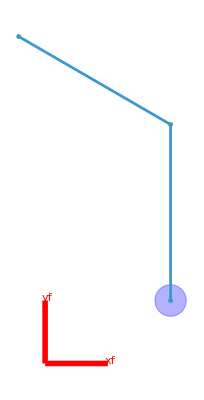

```mathematica
Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],RobotPlot,RF0arrow[1],RF0arrow[2]}]
```

```mathematica
paraml={l1->2.0,l2->3.0};
```

```mathematica
Manipulate[Show[{ListLinePlot[{Ob[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},O1[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},EE[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5}}/.paraml,PlotRange->{{-5,8},{-5,8}},AspectRatio->1,PlotMarkers->{Automatic, 5}]},Block[{r=0.5},Graphics[{EdgeForm[Thick],Blue,Opacity[0.3],Disk[Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},r],Thickness[0.007],Opacity[0.5],Red,Arrowheads[0.04],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 /.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1/.paraml/.paramScheme}}],Blue,Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]-l1 Sin[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Cos[a3]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 Cos[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Sin[a3]/.paraml/.paramScheme}}]}]],RF0arrow[1],RF0arrow[2]],{a1,0,3},{a2,0,3},{a3,0,π/4},{a4,0,π/4},{a5,0,π/4}]
```

## Object

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: xb, yOb, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocityOb of the dof and the contact point:

```mathematica
MfO0=Mrotztrasl[0,{xO[t],yO[t],0}];MfO0//MatrixForm
```

(1 | 0 | 0 | xO[t]
0 | 1 | 0 | yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO0O1=Mrotztrasl[Ω[t],{0,0,0}];MO0O1//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO1O2=Mrotztrasl[γ,{r Cos[γ] ,r Sin[γ],0}];MO1O2//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0 | r Cos[γ]
Sin[γ] | Cos[γ] | 0 | r Sin[γ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MfO1=MfO0.MO0O1;
MfO2=Simplify[MfO0.MO0O1.MO1O2];MfO2//MatrixForm
```

(Cos[γ+Ω[t]] | -Sin[γ+Ω[t]] | 0 | r Cos[γ+Ω[t]]+xO[t]
Sin[γ+Ω[t]] | Cos[γ+Ω[t]] | 0 | r Sin[γ+Ω[t]]+yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactP=(MfO2.{0,0,0,1})[[1;;2]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[γ+Ω[t]]+xO[t]
r Sin[γ+Ω[t]]+yO[t])

(xO'[t]-r Sin[γ+Ω[t]] Ω'[t]
yO'[t]+r Cos[γ+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{xO[t],yO[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[γ+Ω[t]] | r Cos[γ+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

## Dynamics

## Manipulator

### IR method

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

```mathematica
Ixb=1/4 mb r^2;
Iyb=1/4 mb r^2;
Izb=0;
Ix1=1/3m1 l1^2;
Ix2=1/3 m2 l2^2;
```

Inertia frame in the com of the round base:

```mathematica
J00={{Ixb,0,0,0},{0,Iyb,0,0},{0,0,Izb,0},{0,0,0,mb}};J00//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J0f=Simplify[Mf0.J00.Transpose[Mf0]];J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
J11={{Ix1,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J11//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J1f=Simplify[Mf1.J11.Transpose[Mf1]];
```

```mathematica
J22={{Ix2,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J22//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J2f=Simplify[Mf2.J22.Transpose[Mf2]];
```

```mathematica
Wf0=Simplify[D[Mf0,t].Inverse[Mf0]];Wf0//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb=Simplify[D[Mfb,t].Inverse[Mfb]];Wfb//MatrixForm
```

(0 | 0 | 0 | xb'[t]
0 | 0 | 0 | yb'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0=Simplify[D[Mb0,t].Inverse[Mb0]];Wb0//MatrixForm
```

(0 | -θ0'[t] | 0 | 0
θ0'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0Ff=Simplify[Mfb.Wb0.Inverse[Mfb]];Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | yb[t] θ0'[t]
θ0'[t] | 0 | 0 | -xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb+Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Lfbx=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Lfby=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Lb0=Wb0/θ0'[t];
```

```mathematica
Lb0Ff=Simplify[Mf0.Lb0.Inverse[Mf0]];Lb0Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -q1'[t] | 0 | 0
q1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01=W01/q1'[t];
```

```mathematica
L01Ff=Simplify[Mf0.L01.Inverse[Mf0]];L01Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf1=Simplify[D[Mf1,t].Inverse[Mf1]];Wf1//MatrixForm
```

(0 | -q1'[t]-θ0'[t] | 0 | xb'[t]+yb[t] (q1'[t]+θ0'[t])
q1'[t]+θ0'[t] | 0 | 0 | yb'[t]-xb[t] (q1'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];W12//MatrixForm
```

(0 | -q2'[t] | 0 | 0
q2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L12=W12/q2'[t];
L12Ff=Simplify[Mf1.L12.Inverse[Mf1]];L12Ff//MatrixForm
```

(0 | -1 | 0 | l1 Sin[q1[t]+θ0[t]]+yb[t]
1 | 0 | 0 | -l1 Cos[q1[t]+θ0[t]]-xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf2=Simplify[D[Mf2,t].Inverse[Mf2]];Wf2//MatrixForm
```

(0 | -q1'[t]-q2'[t]-θ0'[t] | 0 | l1 Sin[q1[t]+θ0[t]] q2'[t]+xb'[t]+yb[t] (q1'[t]+q2'[t]+θ0'[t])
q1'[t]+q2'[t]+θ0'[t] | 0 | 0 | -l1 Cos[q1[t]+θ0[t]] q2'[t]+yb'[t]-xb[t] (q1'[t]+q2'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
T1=Simplify[1/2Tr[Wf0.J0f.Transpose[Wf0]]];
T2=Simplify[1/2Tr[Wf1.J1f.Transpose[Wf1]]];
T3=Simplify[1/2Tr[Wf2.J2f.Transpose[Wf2]]];
```

The potential energy of body i, denoted by Ui, consists of two parts; one due to the gravity gradient and the other due to the elastic strain energy stored in the flexbible body. The effect of the former is much smaller than the latter and is neglected here. Hence the potential energy of a rigid body is equal to zero.

```mathematica
L=T1+T2+T3;
```

ByOb neglecting the constraints forces (since theyOb don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ0b=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ0b//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕbf=FullSimplify[Mf0.ϕ0b.Transpose[Mf0]];
```

```mathematica
ϕ11=actionMatrix[0,0,τ2-τ3,0,0,0];ϕ11//MatrixForm
ϕ1f=FullSimplify[Mf1.ϕ11.Transpose[Mf1]];ϕ1f//MatrixForm
```

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ϕ22=actionMatrix[0,0,τ3,0,0,0];
ϕ2f=FullSimplify[Mf2.ϕ22.Transpose[Mf2]];
```

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfbx]]
f2=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfby]]
f3=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lb0Ff]]
f4=FullSimplify[PSS[(ϕ1f+ϕ2f),L01Ff]]
f5=Simplify[PSS[(ϕ2f),L12Ff]]
```

Fx Cos[θ0[t]]-Fy Sin[θ0[t]]

Fy Cos[θ0[t]]+Fx Sin[θ0[t]]

τ1

τ2

τ3

```mathematica
eq1=Simplify[D[D[L,xb'[t]],t]-D[L,xb[t]]-f1];
eq2=Simplify[D[D[L,yb'[t]],t]-D[L,yb[t]]-f2];
eq3=Simplify[D[D[L,θ0'[t]],t]-D[L,θ0[t]]-f3];
eq4=Simplify[D[D[L,q1'[t]],t]-D[L,q1[t]]-f4];
eq5=Simplify[D[D[L,q2'[t]],t]-D[L,q2[t]]-f5];
```

```mathematica
{c,A}=FullSimplify[Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M=A[[1;;5,1;;5]];
u=-A[[1;;5,6;;10]];
```

```mathematica
MatrixForm[M]
```

(m1+m2+mb | 0 | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | -1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]]
0 | m1+m2+mb | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]]
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/6 (2 l2^2 m2+2 l1^2 (m1+3 m2)+3 mb r^2+6 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
-1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]] | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]] | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | (l2^2 m2)/3)

```mathematica
MatrixForm[u]
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | 0 | 0
Sin[θ0[t]] | Cos[θ0[t]] | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[c]
```

(1/2 (-l1 (m1+2 m2) Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Cos[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2+l2 m2 Sin[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q1[t]+θ0[t]] Sin[q2[t]] (q1'[t]+q2'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
1/2 l1 l2 m2 Sin[q2[t]] (q1'[t]+θ0'[t])^2)

Equation of motion: Mp^(..)+ c = u

### Classic Lagrangian method

```mathematica
Ob2D=(Mfb.{0,0,0,1})[[1;;2]];
O12D=(Mf1.{-l1/2,0,0,1})[[1;;2]]
EE2D=(Mf2.{-l2/2,0,0,1})[[1;;2]];
```

{1/2 l1 Cos[q1[t]+θ0[t]]+xb[t],1/2 l1 Sin[q1[t]+θ0[t]]+yb[t]}

```mathematica
vb=D[Ob2D,t]
v1=D[O12D,t]
v2=D[EE2D,t]
```

{xb'[t],yb'[t]}

{xb'[t]-1/2 l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t]),yb'[t]+1/2 l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])}

{xb'[t]-l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-1/2 l2 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]),yb'[t]+l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])+1/2 l2 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])}

```mathematica
vbsquare=Simplify[vb[[1]]^2+vb[[2]]^2];
v1square=Simplify[v1[[1]]^2+v1[[2]]^2];
v2square=Simplify[v2[[1]]^2+v2[[2]]^2];
```

Inertia wrt CoM:

```mathematica
Ib=1/2mb r^2;
I1=1/12m1 l1^2;
I2=1/12m2 l2^2;
```

```mathematica
tb=1/2mb vbsquare+1/2Ib θ0'[t]^2;
t1=1/2m1 v1square+1/2I1 (θ0'[t]+q1'[t])^2;
t2=1/2m2 v2square+1/2I2 (θ0'[t]+q1'[t]+q2'[t])^2;
```

```mathematica
lmid=tb+t1+t2;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,xb'[t]],t]-D[lmid,xb[t]]-f1];
eq2Mid=Simplify[D[D[lmid,yb'[t]],t]-D[lmid,yb[t]]-f2];
eq3Mid=Simplify[D[D[lmid,θ0'[t]],t]-D[lmid,θ0[t]]-f3];
eq4Mid=Simplify[D[D[lmid,q1'[t]],t]-D[lmid,q1[t]]-f4];
eq5Mid=Simplify[D[D[lmid,q2'[t]],t]-D[lmid,q2[t]]-f5];
```

```mathematica
{c2,A2}=FullSimplify[Normal@CoefficientArrays[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M2=A2[[1;;5,1;;5]];
u2=-A2[[1;;5,6;;10]];
```

```mathematica
FullSimplify[c2-c]
```

{0,0,0,0,0}

```mathematica
FullSimplify[M[[1]]==M2[[1]]]
FullSimplify[M[[2]]==M2[[2]]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
```

True

True

True

«2 more identical outputs»

## Object

### IR method

```mathematica
IxO=1/4 mO r^2;
IyO=1/4 mO r^2;
IzO=0;
```

```mathematica
JO1O1={{IxO,0,0,0},{0,IyO,0,0},{0,0,IzO,0},{0,0,0,mO}};JO1O1//MatrixForm
```

((mO r^2)/4 | 0 | 0 | 0
0 | (mO r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mO)

```mathematica
J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
JOf=Simplify[MfO1.JO1O1.Transpose[MfO1]];JOf//MatrixForm
```

(1/4 mO (r^2+4 xO[t]^2) | mO xO[t] yO[t] | 0 | mO xO[t]
mO xO[t] yO[t] | 1/4 mO (r^2+4 yO[t]^2) | 0 | mO yO[t]
0 | 0 | 0 | 0
mO xO[t] | mO yO[t] | 0 | mO)

```mathematica
WfO1=Simplify[D[MfO1,t].Inverse[MfO1]];WfO1//MatrixForm
```

(0 | -Ω'[t] | 0 | xO'[t]+yO[t] Ω'[t]
Ω'[t] | 0 | 0 | yO'[t]-xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1=Simplify[D[MO0O1,t].Inverse[MO0O1]];WO0O1//MatrixForm
```

(0 | -Ω'[t] | 0 | 0
Ω'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1Ff=FullSimplify[MfO0.WO0O1.Inverse[MfO0]];WO0O1Ff//MatrixForm
```

(0 | -Ω'[t] | 0 | yO[t] Ω'[t]
Ω'[t] | 0 | 0 | -xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LO0O1Ff=Simplify[WO0O1Ff/Ω'[t]];LO0O1Ff//MatrixForm
```

(0 | -1 | 0 | yO[t]
1 | 0 | 0 | -xO[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LfOx=Lfbx;
LfOy=Lfby;
```

```mathematica
ϕO1O1=actionMatrix[0,0,τO,FOx,FOy,0];
ϕO1O1Ff=FullSimplify[MfO1.ϕO1O1.Transpose[MfO1]];
```

```mathematica
f1O=FullSimplify[PSS[ϕO1O1Ff,LfOx]]
f2O=FullSimplify[PSS[ϕO1O1Ff,LfOy]]
f3O=FullSimplify[PSS[ϕO1O1Ff,LO0O1Ff]]
```

FOx Cos[Ω[t]]-FOy Sin[Ω[t]]

FOy Cos[Ω[t]]+FOx Sin[Ω[t]]

τO

```mathematica
TO=Simplify[1/2Tr[WfO1.JOf.Transpose[WfO1]]];
LO=TO;
```

```mathematica
eq1OIR=Simplify[D[D[LO,xO'[t]],t]-D[L,xO[t]]-f1O];
eq2OIR=Simplify[D[D[LO,yO'[t]],t]-D[L,yO[t]]-f2O];
eq3OIR=Simplify[D[D[LO,Ω'[t]],t]-D[L,Ω[t]]-f3O];
```

```mathematica
{co,Ao}=FullSimplify[Normal@CoefficientArrays[{eq1OIR,eq2OIR,eq3OIR},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}]];
Mo=Ao[[1;;3,1;;3]];
uo=-Ao[[1;;3,4;;6]];
```

```mathematica
Mo//MatrixForm
co//MatrixForm
uo//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

### Classic method

```mathematica
Iz=1/2mO r^2;
```

```mathematica
T=1/2 mO(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1O=Simplify[D[D[T,xO'[t]],t]-D[T,xO[t]]-f1O];
eq2O=Simplify[D[D[T,yO'[t]],t]-D[T,yO[t]]-f2O];
eq3O=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-f3O];
```

```mathematica
{co2,Ao2}=Normal@CoefficientArrays[{eq1O,eq2O,eq3O},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}];
Mo2=Ao2[[1;;3,1;;3]];
uo2=-Ao2[[1;;3,4;;6]];
```

```mathematica
Mo2//MatrixForm
co2//MatrixForm
uo2//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=Transpose[Jo].Inverse[Jo.Transpose[Jo]]//Simplify;pseudoInverseJo//MatrixForm
```

((2+r^2+r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2)) | (r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2)
(r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2) | (2+r^2-r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2))
-(r Sin[γ+Ω[t]])/(1+r^2) | (r Cos[γ+Ω[t]])/(1+r^2))

```mathematica
G=M+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J//FullSimplify ;
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t]};
p'=D[p,t];
```

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
H=M. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'//Simplify;
```

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
Transpose[J[[1;;2]]/.param/.paramScheme]//MatrixForm
```

(1 | 0
0 | 1
-8.385 | -4.84108
-8.385 | -4.84108
-2.795 | -4.84108)

```mathematica
Chop[Inverse[G]/.param/.paramScheme/.Ω[t]->contactCondition]//MatrixForm
```

(2.38195×10^-6 | -1.51092×10^-10 | 0 | 4.34371×10^-7 | -4.3868×10^-7
-1.51092×10^-10 | 2.3799×10^-6 | 0 | -2.26976×10^-7 | 7.16898×10^-7
0 | 0 | 0.000330904 | -0.000330904 | 0
4.34371×10^-7 | -2.26976×10^-7 | -0.000330904 | 0.000343394 | -0.0000189624
-4.3868×10^-7 | 7.16898×10^-7 | 0 | -0.0000189624 | 0.0000394065)

```mathematica
pf'=Inverse[G].H ;
```

Final values of the satellite after the impact:

```mathematica
ψf'=pseudoInverseJo.J.pf';
```

### Initial conditions

After the capture, we assume that the object is now perfectlyOb attached to the EE, hence the contact point’s variables coincides with the ones of the EE. We also assume that the spinning velocityOb is resetted:

```mathematica
EEi=EE[[1;;2]]/.param/.paramScheme
```

{-0.841082,10.385}

Condition for alignment of the object with the EE:

```mathematica
contactCondition=(θ00+q10+q20+π-(γ/.param))
```

5.25959

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.103923+xO[t],-0.06+yO[t]}

```mathematica
objectPosI=(Solve[{EEi[[1]]==(contactP/.param/.Ω[t]->contactCondition)[[1]],EEi[[2]]==(contactP/.param/.Ω[t]->contactCondition)[[2]]},{xO[t],yO[t]}])[[1]]
```

{xO[t]→-0.945005,yO[t]→10.445}

Let’s suppose initial zero velocities of the BM system.

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/3,xb[t]→4,yb[t]→2}

```mathematica
initialConditions1={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->1,yO'[t]->0,Ω'[t]->0.01};
initialConditions2={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->0,yO'[t]->-1,Ω'[t]->0.01};
```

```mathematica
pf1'=pf'/.initialConditions1/.param/.paramScheme//Chop
pf2'=pf'/.initialConditions2/.param/.paramScheme//Chop
```

{-0.000102493,-0.000302925,0,-0.153968,0.144454}

{-0.0000604807,-0.0000222822,0,-0.0908562,0.288955}

```mathematica
ψf1'=ψf'/.initialConditions1/.param/.paramScheme//Chop
ψf2'=ψf'/.initialConditions2/.param/.paramScheme//Chop
```

{0.88374,0.0398139,0.057162}

{-0.0398025,-0.948542,-0.100964}

```mathematica
a=((Jo.ψf')/.initialConditions1/.param/.paramScheme)
```

{0.88717,0.0457543}

```mathematica
b=((J.pf')/.initialConditions1/.param/.paramScheme)
```

{0.88717,0.0457543}

```mathematica
a-b//Chop
```

{0,0}

## Post-impact

-Graphics-

```mathematica
EEp=EE[[1;;2]]/.param;
```

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.103923+xO[t],-0.06+yO[t]}

```mathematica
contactConditionP=(θ0[t]+q1[t]+q2[t]+π-(γ/.param));
```

```mathematica
objectPosP=(Solve[{EE[[1]]==(contactP/.param/.Ω[t]->contactConditionP)[[1]],EE[[2]]==(contactP/.param/.Ω[t]->contactConditionP)[[2]]},{xO[t],yO[t]}])[[1]];
```

```mathematica
ψp={objectPosP[[1,2]],objectPosP[[2,2]],contactConditionP};
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]}
```

{xO[t]→-1. (-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]]+0.12 Cos[3.14159+q1[t]+q2[t]+θ0[t]]-xb[t]),yO[t]→-1. (-l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]]+0.12 Sin[3.14159+q1[t]+q2[t]+θ0[t]]-yb[t]),Ω[t]→2.64159+q1[t]+q2[t]+θ0[t]}

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

Since we are considering only rigid bodies, there is no contribution of the elastic part (no matrix K).

```mathematica
Mp=M+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp;
```

```mathematica
Dimensions[eqMotion]
```

{5}

### Simulation with no control

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/3,xb[t]→4,yb[t]→2}

```mathematica
NDinitialCondition1={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf1'[[1]],yb'[0]==pf1'[[2]],θ0'[0]==pf1'[[3]],q1'[0]==pf1'[[4]],q2'[0]==pf1'[[5]]}
NDinitialCondition2={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf2'[[1]],yb'[0]==pf2'[[2]],θ0'[0]==pf2'[[3]],q1'[0]==pf2'[[4]],q2'[0]==pf2'[[5]]}
```

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/3,xb'[0]==-0.000102493,yb'[0]==-0.000302925,θ0'[0]==0,q1'[0]==-0.153968,q2'[0]==0.144454}

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/3,xb'[0]==-0.0000604807,yb'[0]==-0.0000222822,θ0'[0]==0,q1'[0]==-0.0908562,q2'[0]==0.288955}

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

```mathematica
imgSize=475;
imagePadding={{100,10},{25,10}};
```

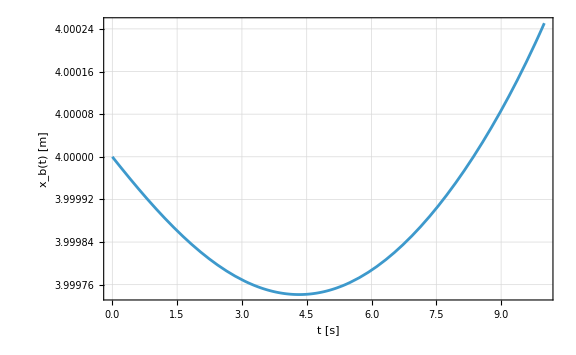
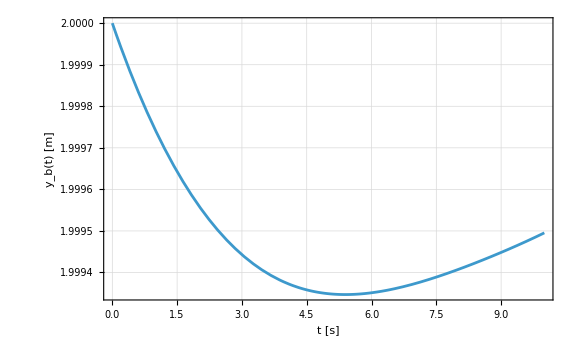
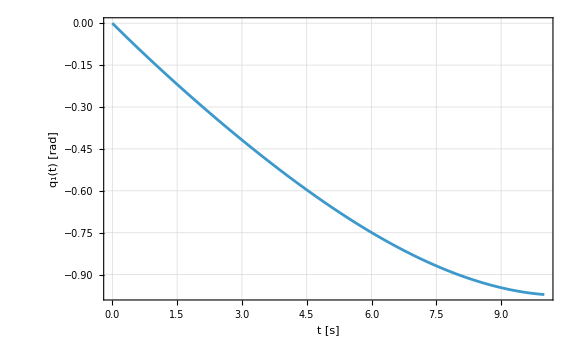
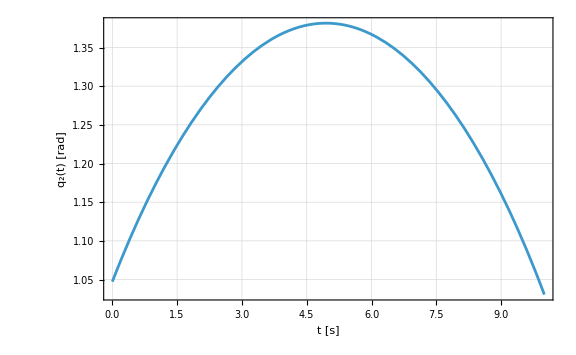
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion1[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

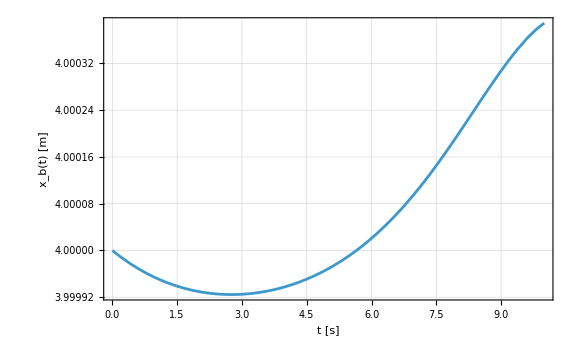
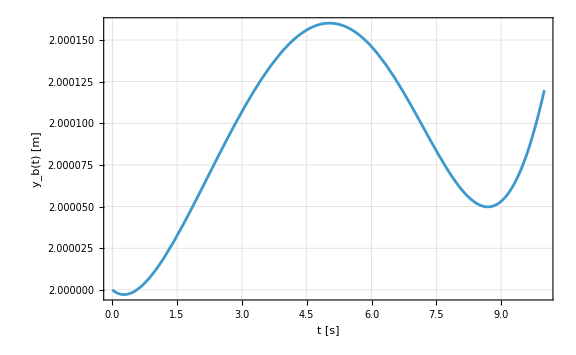
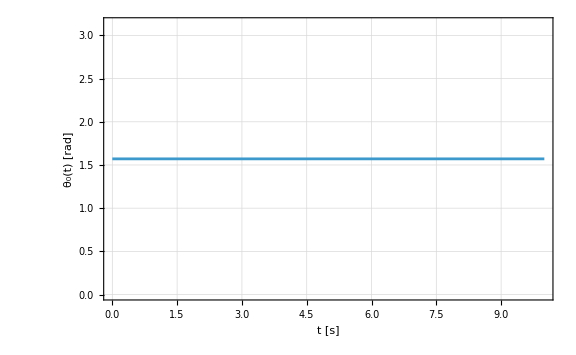
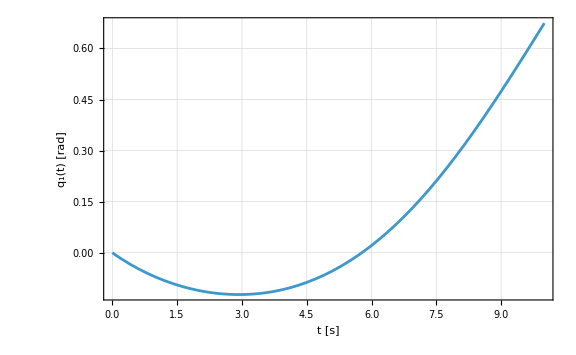
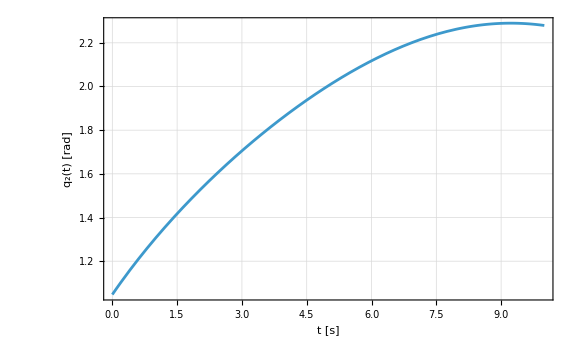

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[solMotion2[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10}
{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10}
```

{{4.00025,1.9995},{8.61508,5.15409},{8.28338,10.7342}}

{{4.00039,2.00012},{0.510317,6.36676},{-0.533639,0.875102}}

```mathematica
RobotPlotAfter1=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

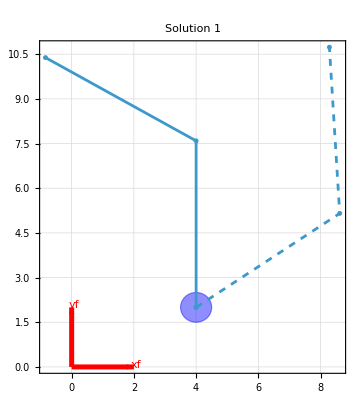
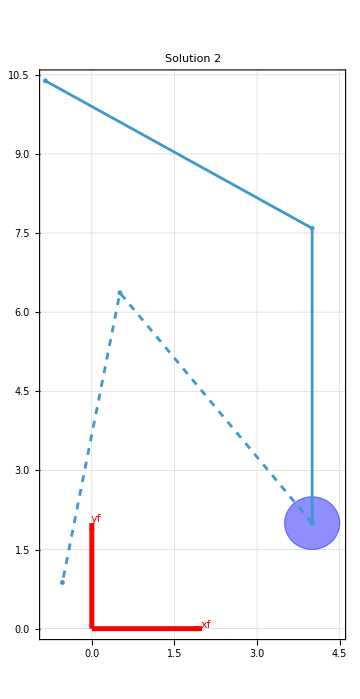

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

### Simulation with control

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=1IdentityMatrix[3];
Kv0=2 Sqrt[Kp];
Kv1=2 0.5 Sqrt[Kp];
Kv2=2 1.5 Sqrt[Kp];
```

```mathematica
pd={θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0};
```

{π/2,0,π/3}

```mathematica
p3={θ0[t],q1[t],q2[t]};
p3'=D[p3,t];
```

```mathematica
Mtt=Mp[[1;;2,1;;2]];
Mtr=Mp[[1;;2,3;;5]];
Mrt=Mp[[3;;5,1;;2]];
Mrr=Mp[[3;;5,3;;5]];
Ct=Cp[[1;;2]];
Cr=Cp[[3;;5]];
```

```mathematica
Mhat=Mrr-Mrt.Inverse[Mtt].Mtr;
Chat=Cr-Mrt.Inverse[Mtt].Ct;
```

```mathematica
U0=-Mhat.(Kv0.(p3'-pd')+Kp.(p3-pd))+Chat;
U1=-Mhat.(Kv1.(p3'-pd')+Kp.(p3-pd))+Chat;
U2=-Mhat.(Kv2.(p3'-pd')+Kp.(p3-pd))+Chat;
```

```mathematica
eqMotionControl10=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl20=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl30=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U0[[1]];
eqMotionControl40=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U0[[2]];
eqMotionControl50=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U0[[3]];
```

```mathematica
eqMotionControl11=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl21=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl31=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U1[[1]];
eqMotionControl41=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U1[[2]];
eqMotionControl51=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U1[[3]];
```

```mathematica
eqMotionControl12=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl22=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl32=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U2[[1]];
eqMotionControl42=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U2[[2]];
eqMotionControl52=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U2[[3]];
```

```mathematica
solMotionControl10=NDSolve[{(eqMotionControl10/.param)==0,(eqMotionControl20/.param)==0,(eqMotionControl30/.param)==0,(eqMotionControl40/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl20=NDSolve[{(eqMotionControl10/.param)==0,(eqMotionControl20/.param)==0,(eqMotionControl30/.param)==0,(eqMotionControl40/.param)==0,(eqMotionControl50/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl11=NDSolve[{(eqMotionControl11/.param)==0,(eqMotionControl21/.param)==0,(eqMotionControl31/.param)==0,(eqMotionControl41/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl21=NDSolve[{(eqMotionControl11/.param)==0,(eqMotionControl21/.param)==0,(eqMotionControl31/.param)==0,(eqMotionControl41/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl12=NDSolve[{(eqMotionControl12/.param)==0,(eqMotionControl22/.param)==0,(eqMotionControl32/.param)==0,(eqMotionControl42/.param)==0,(eqMotionControl52/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl22=NDSolve[{(eqMotionControl12/.param)==0,(eqMotionControl22/.param)==0,(eqMotionControl32/.param)==0,(eqMotionControl42/.param)==0,(eqMotionControl52/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

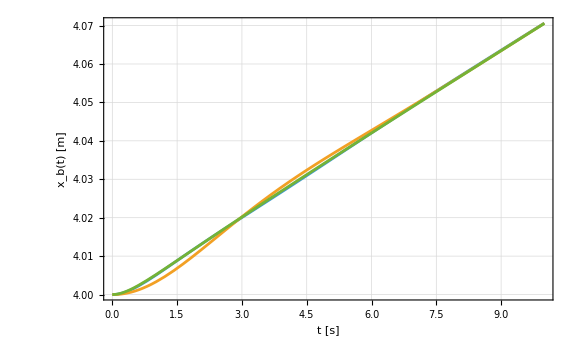
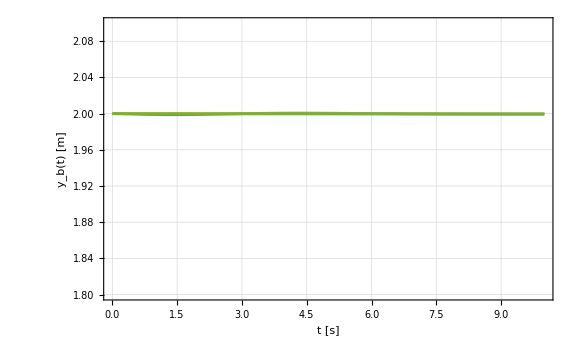
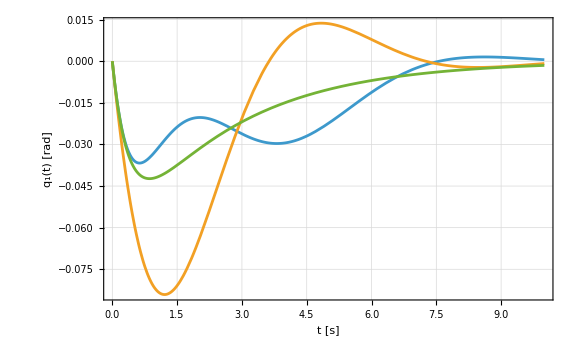
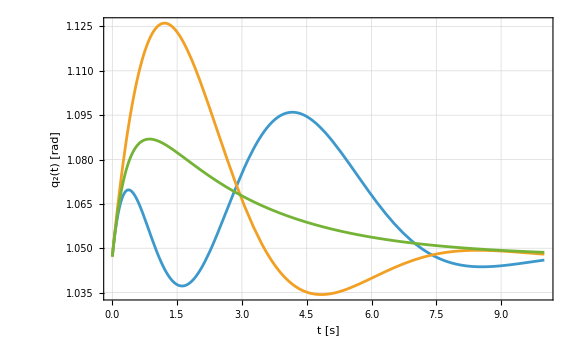
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[{solMotionControl10[[1,2]],solMotionControl11[[1,2]],solMotionControl12[[1,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[2,2]],solMotionControl11[[2,2]],solMotionControl12[[2,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}},ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[3,2]],solMotionControl11[[3,2]],solMotionControl12[[3,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl10[[4,2]],solMotionControl11[[4,2]],solMotionControl12[[4,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding,PlotRange->All],
Plot[{solMotionControl10[[5,2]],solMotionControl11[[5,2]],solMotionControl12[[5,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

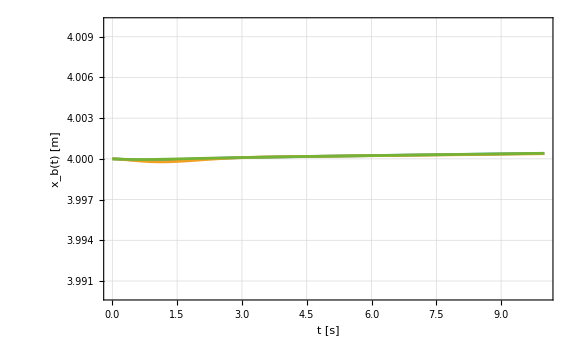
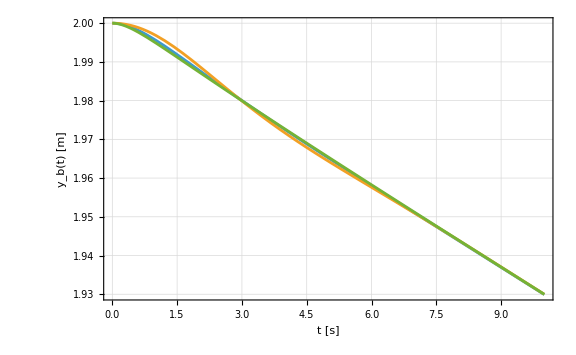
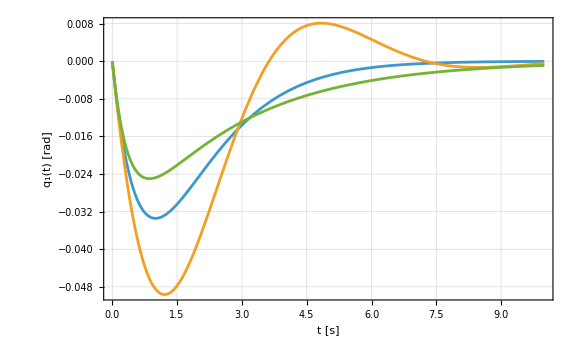
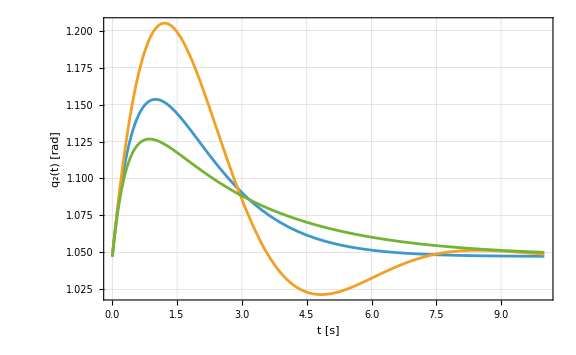
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[{solMotionControl20[[1,2]],solMotionControl21[[1,2]],solMotionControl22[[1,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{3.99,4.01}},ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[2,2]],solMotionControl21[[2,2]],solMotionControl22[[2,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[3,2]],solMotionControl21[[3,2]],solMotionControl22[[3,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[4,2]],solMotionControl21[[4,2]],solMotionControl22[[4,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding],
Plot[{solMotionControl20[[5,2]],solMotionControl21[[5,2]],solMotionControl22[[5,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]}]
```

### Simulation with uknown mass

```mathematica
test=5000;
```

```mathematica
series[f_,v_,v0_,order_]:=Module[{e},Expand[Normal[Series[f/.Thread[v->v0+e*v],{e,0,order}]]/.e->1]]
```

```mathematica
Kp=1IdentityMatrix[2];
Kv0=1.999*Sqrt[Kp];
```

```mathematica
pd0={q100,q200};
```

```mathematica
p2={q1[t],q2[t]};
p2'=D[p2,t];
```

```mathematica
pd={q1[t],q2[t]}/.paramScheme;
pd'={0,0};
```

```mathematica
eqMotionStim4=series[(Mp[[4,1;;5]].D[p,t,t]+Cp[[4]])/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,θ0[t]->π/2,θ0'[t]->0},{q1[t],q2[t],q1'[t],q2'[t],q1''[t],q2''[t]},{q100,q200,0,0,0,0},1];
eqMotionStim5=series[(Mp[[5,1;;5]].D[p,t,t]+Cp[[5]])/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,θ0[t]->π/2,θ0'[t]->0},{q1[t],q2[t],q1'[t],q2'[t],q1''[t],q2''[t]},{q100,q200,0,0,0,0},1];
```

```mathematica
{c,Mlin}=Normal@CoefficientArrays[{eqMotionStim4,eqMotionStim5},{q1''[t],q2''[t]}];
```

```mathematica
Ulin=-Mlin.(Kv0.(p2'-pd')+Kp.(p2-pd0));
```

```mathematica
linearizedEq1Real=((eqMotionStim4/.param)-Ulin[[1]])//Simplify;
linearizedEq2Real=((eqMotionStim5/.param)-Ulin[[2]])//Simplify;
```

```mathematica
linearSol1=Simplify@Chop@DSolve[{(linearizedEq1Real/.q100->q10/.q200->q20/.mO->test)==0,(linearizedEq2Real/.q100->q10/.q200->q20/.mO->test)==0,q1[0]==q10,q1'[0]==pf1'[[4]],q2[0]==q20,q2'[0]==pf1'[[5]]},{q1[t],q2[t]},t][[1]];
linearSol2=Simplify@Chop@DSolve[{(linearizedEq1Real/.q100->q10/.q200->q20/.mO->test)==0,(linearizedEq2Real/.q100->q10/.q200->q20/.mO->test)==0,q1[0]==q10,q1'[0]==pf2'[[4]],q2[0]==q20,q2'[0]==pf2'[[5]]},{q1[t],q2[t]},t][[1]];
```

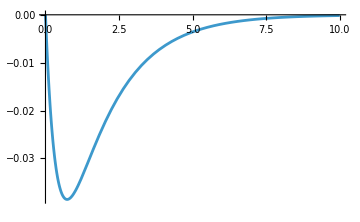
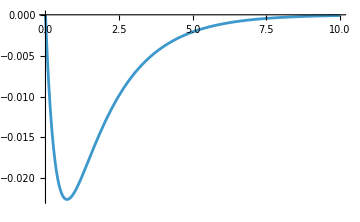

```mathematica
Row[{Plot[{q1[t]/.linearSol1},{t,0,10},PlotRange->{{0,10},All},ImageSize->Medium],Plot[{q1[t]/.linearSol2},{t,0,10},PlotRange->{{0,10},All},ImageSize->Medium]}]
```

```mathematica
Kp=1IdentityMatrix[3];
Kv0=2 Sqrt[Kp];
```

```mathematica
pd={θ0[t],q1[t],q2[t]}/.paramScheme;
pd'={0,0,0};
```

```mathematica
Mpstim=Mp/.mO->test;
Cpstim=Cp/.mO->test;
```

```mathematica
Mttstim=Mpstim[[1;;2,1;;2]];
Mtrstim=Mpstim[[1;;2,3;;5]];
Mrtstim=Mpstim[[3;;5,1;;2]];
Mrrstim=Mpstim[[3;;5,3;;5]];
Ctstim=Cpstim[[1;;2]];
Crstim=Cpstim[[3;;5]];
```

```mathematica
Mhatstim=Mrrstim-Mrtstim.Inverse[Mttstim].Mtrstim;
Chatstim=Crstim-Mrtstim.Inverse[Mttstim].Ctstim;
```

```mathematica
U=-Mhatstim.(Kv0.(p3'-pd')+Kp.(p3-pd))+Chatstim;
```

```mathematica
eqMotionControlStim1=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControlStim2=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControlStim3=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U[[1]];
eqMotionControlStim4=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U[[2]];
eqMotionControlStim5=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U[[3]];
```

```mathematica
solMotionControl1=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15}, Method->{"EquationSimplification"->"Residual"}][[1]]
solMotionControl2=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15}, Method->{"EquationSimplification"->"Residual"}][[1]];
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

```mathematica
solMotionControl1Data=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition1},{xb,yb,θ0,q1,q2},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl2Data=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition2},{xb,yb,θ0,q1,q2},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]];
```

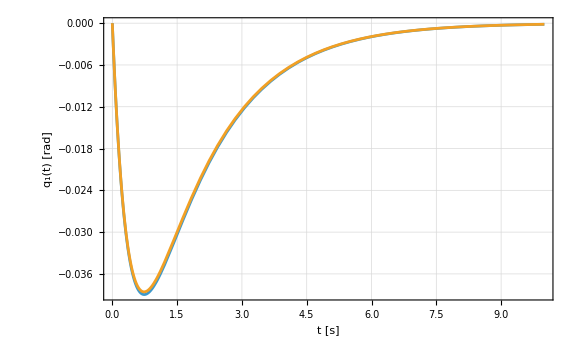

```mathematica
Plot[{solMotionControl1[[4,2]],q1[t]/.linearSol1},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]
```

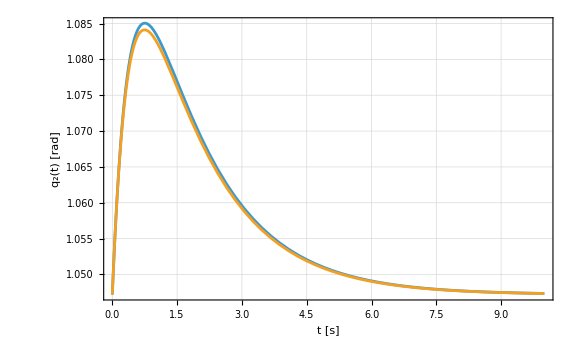

```mathematica
Plot[{solMotionControl1[[5,2]],q2[t]/.linearSol1},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,ImageSize->imgSize,ImagePadding->imagePadding]
```

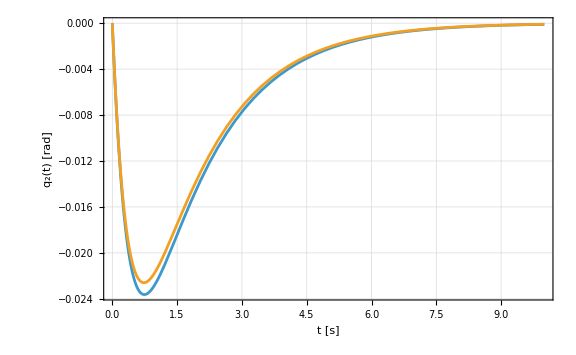

```mathematica
Plot[{solMotionControl2[[4,2]],q1[t]/.linearSol2},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

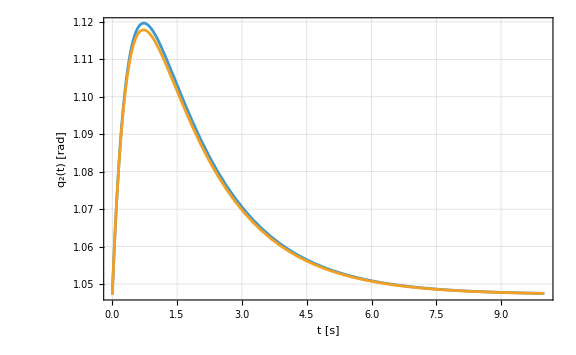

```mathematica
Plot[{solMotionControl2[[5,2]],q2[t]/.linearSol2},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

Natural frequencies of the system:

```mathematica
{Ccoupled,Alin}=Normal@CoefficientArrays[{linearizedEq1Real,linearizedEq2Real},{q1''[t],q2''[t],q1[t],q2[t]}];
```

```mathematica
Mcoupled=Alin[[1;;2,1;;2]];
Kcoupled=Alin[[1;;2,3;;4]];
```

```mathematica
(Mcoupled.{q1''[t],q2''[t]}+Ccoupled+Kcoupled.{q1[t],q2[t]})[[1]]/.q100->q10/.q200->q20/.mO->2000
linearizedEq1Real/.q100->q10/.q200->q20/.mO->2000/.q2[t]->q20/.q2'[t]->0/.q2''[t]->0//Simplify
```

-101138.+203850. q1[t]+96579.5 q2[t]+407496. q1'[t]+193063. q2'[t]+295620. q1''[t]+142135. q2''[t]

0.+203850. q1[t]+407496. q1'[t]+295620. q1''[t]

```mathematica
zzz=Simplify[DSolve[{(linearizedEq2Real/.q100->q10/.q200->q20/.q1[t]->q10/.q1'[t]->0/.q1''[t]->0)==0,q2[0]==q20,q2'[0]==pf1'[[5]]},q2[t],t][[1]]]
ccc=DSolve[{(linearizedEq1Real/.q100->q10/.q200->q20/.q2[t]->q20/.q2'[t]->0/.q2''[t]->0)==0,q1[0]==q10,q1'[0]==pf1'[[4]]},q1[t],t][[1]]
```

{q2[t]→(-1421.71+4.34632×10^-7 mO^4-734.844 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)+mO (-40.98-21.4261 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2))+mO^2 (-0.389087-0.208243 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2))+mO^3 (-0.00117109-0.000674645 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2))+ⅇ^(-0.5 (0.0662857+0.000644238 mO+√(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)) t) (101.367+0.0000930629 mO^3-1529.25 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)+mO (2.95559-29.7258 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2))+mO^2 (0.0287257-0.144454 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)))+ⅇ^(0.5 (-0.0662857-0.000644238 mO+√(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)) t) (-101.367-0.0000930629 mO^3+1529.25 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)+mO^2 (-0.0287257+0.144454 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2))+mO (-2.95559+29.7258 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2))))/((102.89+1. mO)^2 √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2) (-0.0662857-0.000644238 mO+1. √(-0.128244-0.00120371 mO+4.15043×10^-7 mO^2)))}

{q1[t]→(0.153968 (1. ⅇ^(1/2 (-0.137346-0.000620551 mO-√(-0.255966-0.00107126 mO+3.85084×10^-7 mO^2)) t)-1. ⅇ^(1/2 (-0.137346-0.000620551 mO+√(-0.255966-0.00107126 mO+3.85084×10^-7 mO^2)) t)))/(√(-0.255966-0.00107126 mO+3.85084×10^-7 mO^2))}

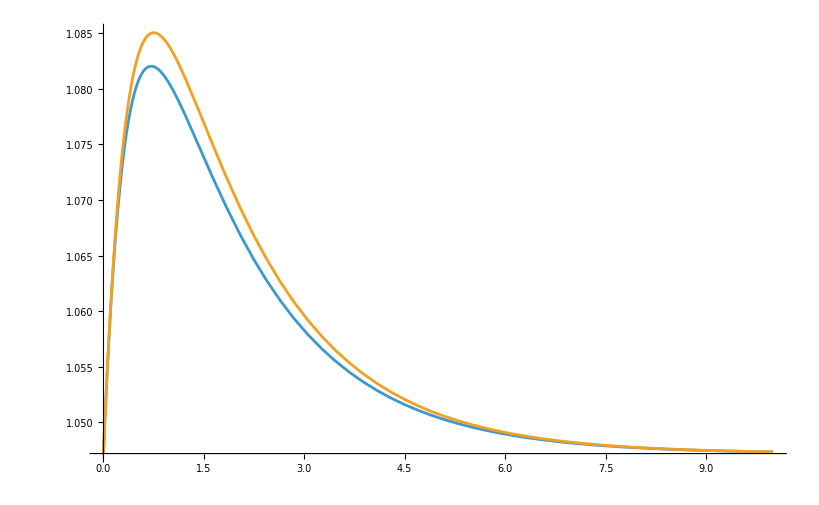

```mathematica
Plot[{q2[t]/.zzz/.mO->test,q2[t]/.solMotionControl1},{t,0,10}]
```

```mathematica
Chop[Mp/.param/.paramScheme]//MatrixForm
```

(423304. | -36.4885 | -27736.5 | -27736.5 | -8568.72
-36.4885 | 423262. | -14637.5 | -14637.5 | -14841.5
-27736.5 | -14637.5 | 298642. | 295620. | 142135.
-27736.5 | -14637.5 | 295620. | 295620. | 142135.
-8568.72 | -14841.5 | 142135. | 142135. | 94235.9)

```mathematica
Chop@FullSimplify[Mcoupled]/.q200->q20//MatrixForm
```

(295620. | 142135.
142135. | 94235.9)

```mathematica
Chop@FullSimplify[Kcoupled/.mO->4000/.q200->q20/.q100->q10]//MatrixForm
```

(387389. | 187691.
187691. | 124606.)

```mathematica
Sqrt[124606/94235.93617214322]
```

1.1499

```mathematica
solfreq=Solve[Det[Kcoupled-ω^2Mcoupled]==0,ω];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solfreq/.q100->q10/.q200->q20/.mO->2000
```

{{ω→-0.843643+0. ⅈ},{ω→0.843643+0. ⅈ},{ω→-0.82309+0. ⅈ},{ω→0.82309+0. ⅈ}}

```mathematica
freq1=Re@solfreq[[4,1,2]];
freq2=Re@solfreq[[2,1,2]];
```

```mathematica
freq1/.q100->q10/.q200->q20/.mO->4000
freq2/.q100->q10/.q200->q20/.mO->4000
```

1.13502

1.15001

```mathematica
Solve[(Det[Kcoupled-ω^2Mcoupled]/.q100->q10/.q200->q20/.mO->4000)==0,ω]
```

{{ω→-1.15001},{ω→-1.13502},{ω→1.13502},{ω→1.15001}}

Modal shapes:

```mathematica
Chop[(Kcoupled-freq1^2Mcoupled)/.mO->4000/.q100->q10/.q200->q20,10^-5]
```

{{6552.13,4582.73},{4582.73,3205.28}}

```mathematica
Solve[((Chop[(Kcoupled-freq1^2Mcoupled)[[2]]/.q100->q10/.q200->q20/.mO->4000,10^-5]).{u11,u12})==0,{u11,u12}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{u12→0.-1.42974 u11}}

```mathematica
parametricMode=Solve[(((Kcoupled-freq1^2Mcoupled)[[1]]).{1,u12})==0,u12]
```

$Aborted

```mathematica
parametricMode[[1,1,2]]/.mO->2000/.q100->q10/.q200->q20
```

-6.

```mathematica
testone=parametricMode[[1,1,2]]/.mO->3000
```

```mathematica
xxx=testone/.q200->π/2;
```

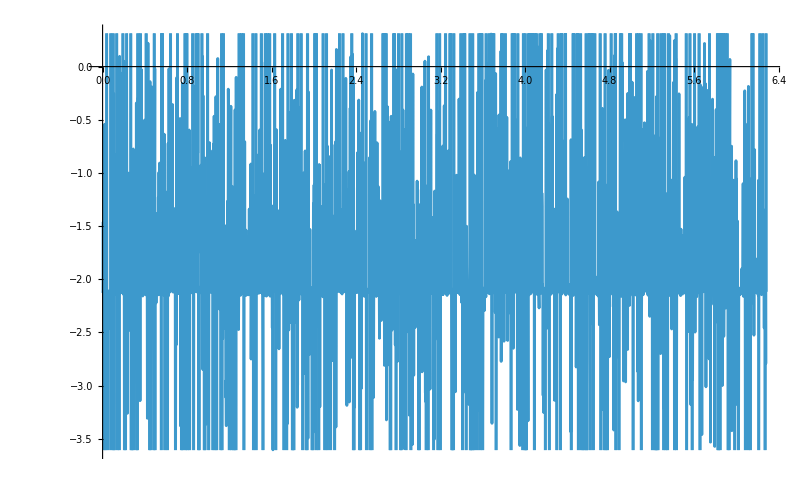

```mathematica
Plot[xxx,{q100,0,2π}]
```

```mathematica
parametricMode11=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->q10/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode21=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->q10/.q200->0).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode31=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->q10/.q200->π/6).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode41=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->q10/.q200->π/4).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode51=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->q10/.q200->π/3).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
parametricMode12=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->q10/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode22=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->q10/.q200->0).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode32=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->q10/.q200->π/6).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode42=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->q10/.q200->π/4).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode52=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->q10/.q200->π/3).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

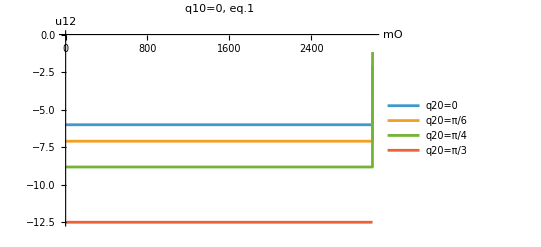

```mathematica
Plot[{parametricMode21,parametricMode31,parametricMode41,parametricMode51},{mO,0,3000},AxesLabel->{"mO", "u12"},PlotLabel->"q10=0, eq.1",PlotLegends->{"q20=0","q20=π/6","q20=π/4","q20=π/3"}]
```

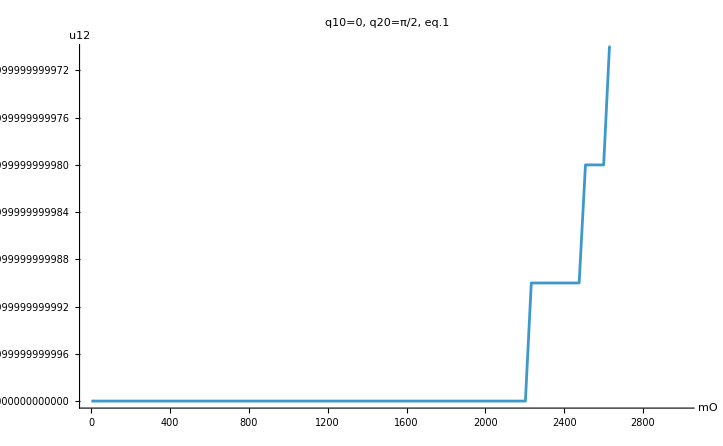

```mathematica
Plot[parametricMode11,{mO,0,3000},AxesLabel->{"mO", "u12"},PlotLabel->"q10=0, q20=π/2, eq.1"]
```

```mathematica
parametricMode11/.mO->3000
```

-2.04933

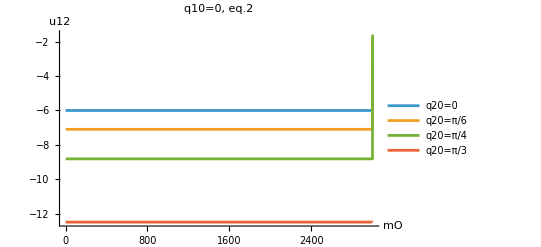

```mathematica
Plot[{parametricMode22,parametricMode32,parametricMode42,parametricMode52},{mO,0,3000},AxesLabel->{"mO", "u12"},PlotLabel->"q10=0, eq.2",PlotLegends->{"q20=0","q20=π/6","q20=π/4","q20=π/3"}]
```

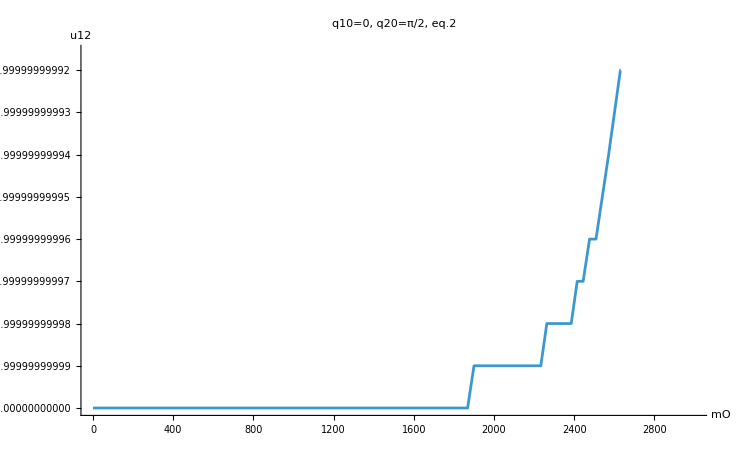

```mathematica
Plot[parametricMode12,{mO,0,3000},AxesLabel->{"mO", "u12"},PlotLabel->"q10=0, q20=π/2, eq.2"]
```

```mathematica
parametricMode11=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->q10/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode21=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->q10/.q200->0).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode31=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->q10/.q200->π/6).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode41=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->q10/.q200->π/4).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode51=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->q10/.q200->π/3).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
parametricMode12=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->q10/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode22=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->q10/.q200->0).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode32=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->q10/.q200->π/6).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode42=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->q10/.q200->π/4).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode52=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->q10/.q200->π/3).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

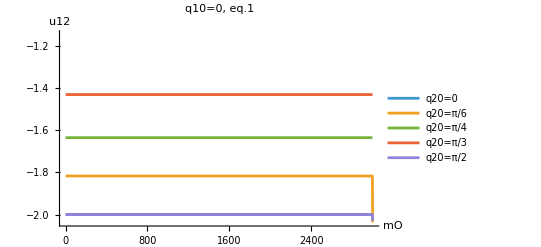

```mathematica
Plot[{parametricMode21,parametricMode31,parametricMode41,parametricMode51,parametricMode11},{mO,0,3000},AxesLabel->{"mO", "u12"},PlotLabel->"q10=0, eq.1",PlotLegends->{"q20=0","q20=π/6","q20=π/4","q20=π/3","q20=π/2"}]
```

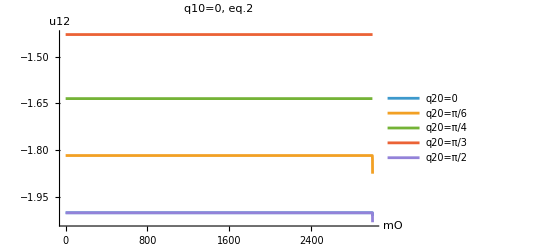

```mathematica
Plot[{parametricMode22,parametricMode32,parametricMode42,parametricMode52,parametricMode11},{mO,0,3000},AxesLabel->{"mO", "u12"},PlotLabel->"q10=0, eq.2",PlotLegends->{"q20=0","q20=π/6","q20=π/4","q20=π/3","q20=π/2"}]
```

```mathematica
parametricMode11=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->0/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode21=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->π/6/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode31=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->π/4/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode41=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->π/3/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode51=Solve[((((Kcoupled-freq1^2Mcoupled)[[1]])/.q100->π/2/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
parametricMode12=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->0/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode22=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->π/6/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode32=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->π/4/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode42=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->π/3/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode52=Solve[((((Kcoupled-freq1^2Mcoupled)[[2]])/.q100->π/2/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

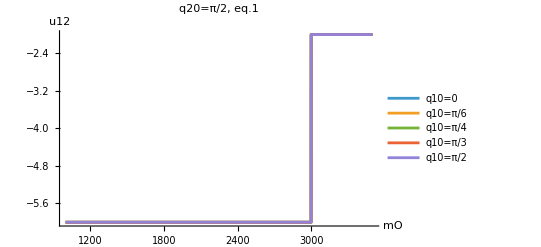

```mathematica
Plot[{parametricMode11,parametricMode21,parametricMode31,parametricMode41,parametricMode51},{mO,1000,3500},AxesLabel->{"mO", "u12"},PlotLabel->"q20=π/2, eq.1",PlotLegends->{"q10=0","q10=π/6","q10=π/4","q10=π/3","q10=π/2"},PlotRange->All]
```

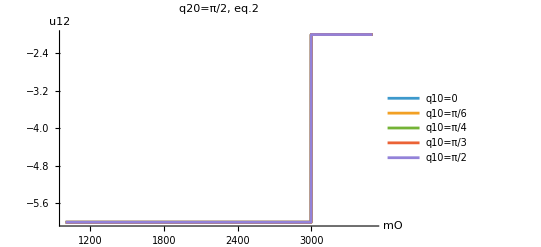

```mathematica
Plot[{parametricMode12,parametricMode22,parametricMode32,parametricMode42,parametricMode52},{mO,1000,3500},AxesLabel->{"mO", "u12"},PlotLabel->"q20=π/2, eq.2",PlotLegends->{"q10=0","q10=π/6","q10=π/4","q10=π/3","q10=π/2"},PlotRange->All]
```

```mathematica
parametricMode11=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->0/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode21=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->π/6/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode31=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->π/4/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode41=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->π/3/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode51=Solve[((((Kcoupled-freq2^2Mcoupled)[[1]])/.q100->π/2/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
parametricMode12=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->0/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode22=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->π/6/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode32=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->π/4/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode42=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->π/3/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
parametricMode52=Solve[((((Kcoupled-freq2^2Mcoupled)[[2]])/.q100->π/2/.q200->q20).{u11,u12}//Simplify)==0,{u11,u12}][[1,1,2]]/.u11->1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

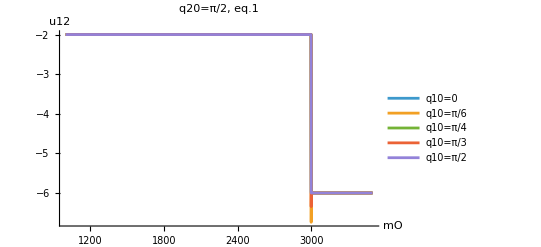

```mathematica
Plot[{parametricMode11,parametricMode21,parametricMode31,parametricMode41,parametricMode51},{mO,1000,3500},AxesLabel->{"mO", "u12"},PlotLabel->"q20=π/2, eq.1",PlotLegends->{"q10=0","q10=π/6","q10=π/4","q10=π/3","q10=π/2"},PlotRange->All]
```

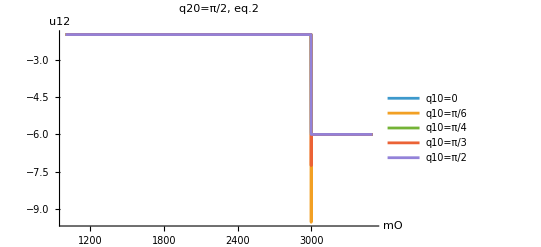

```mathematica
Plot[{parametricMode12,parametricMode22,parametricMode32,parametricMode42,parametricMode52},{mO,1000,3500},AxesLabel->{"mO", "u12"},PlotLabel->"q20=π/2, eq.2",PlotLegends->{"q10=0","q10=π/6","q10=π/4","q10=π/3","q10=π/2"},PlotRange->All]
```

```mathematica
Mp/.param/.paramScheme//MatrixForm
```

(423241. | 1.54795×10^-14 | -35951.9 | -35951.9 | -17137.4
1.54795×10^-14 | 423325. | -1.73061×10^-13 | -1.73061×10^-13 | -8.65306×10^-14
-35951.9 | -1.73061×10^-13 | 392465. | 389443. | 190034.
-35951.9 | -1.73061×10^-13 | 389443. | 389443. | 190034.
-17137.4 | -8.65306×10^-14 | 190034. | 190034. | 94235.9)

```mathematica
Kcoupled/.q100->q10/.q200->q20/.mO->test//MatrixForm
Mcoupled/.q100->q10/.q200->q20/.mO->test//MatrixForm
```

(267961. | 129294.
129294. | 63865.6)

(389443. | 190034.
190034. | 94235.9)

```mathematica
Kcoupled[[1,2]]-freq1^2Mcoupled[[1,2]]/.q100->q10/.q200->q20/.mO->test
```

758.442

```mathematica
(Kcoupled-(freq1^2)Mcoupled)/.q100->q10/.q200->q20/.mO->test//MatrixForm
```

(4550.65 | 758.442
758.442 | 126.407)

#### Nonlinearfit Symbolic Form

```mathematica
q11Data=Transpose@{solMotionControl1Data[[4,2,3]][[1]],solMotionControl1Data[[4,2,4,3,1;;Dimensions[solMotionControl1Data[[4,2,4,3]]][[1]];;3]]};
q21Data=Transpose@{solMotionControl1Data[[5,2,3]][[1]],solMotionControl1Data[[5,2,4,3,1;;Dimensions[solMotionControl1Data[[5,2,4,3]]][[1]];;3]]};
q12Data=Transpose@{solMotionControl2Data[[4,2,3]][[1]],solMotionControl2Data[[4,2,4,3,1;;Dimensions[solMotionControl2Data[[4,2,4,3]]][[1]];;3]]};
q22Data=Transpose@{solMotionControl2Data[[5,2,3]][[1]],solMotionControl2Data[[5,2,4,3,1;;Dimensions[solMotionControl2Data[[5,2,4,3]]][[1]];;3]]};
```

```mathematica
eqApprox1=Chop[Collect[Expand[eqMotionControlStim4/.paramScheme/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q2''[t]->0,θ0[t]->π/2,q2[t]->π/2,θ0'[t]->0,q2'[t]->0}],{q1[t],q1'[t],q1''[t]}]]/.q1'[t]^2->0
eqApprox2=Chop[Collect[Expand[eqMotionControlStim5/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q1''[t]->0,θ0[t]->π/2,q1[t]->0,θ0'[t]->0,q1'[t]->0}],{q2[t],q2'[t],q2''[t]}]]
```

532942. q1'[t]+(24998.5+121.482 mO) q1''[t]

```mathematica
sol11=DSolve[{eqApprox1==0,q1[0]==q10,q1'[0]==pf1'[[4]]},q1[t],t][[1]];
sol21=DSolve[{eqApprox2==0,q2[0]==q20,q2'[0]==pf1'[[5]]},q2[t],t][[1]];
sol12=DSolve[{eqApprox1==0,q1[0]==q10,q1'[0]==pf2'[[4]]},q1[t],t][[1]];
sol22=DSolve[{eqApprox2==0,q2[0]==q20,q2'[0]==pf2'[[5]]},q2[t],t][[1]];
```

```mathematica
table1=Table[Plot[q1[t]/.sol11/.mO->300*i,{t,0,10},PlotRange->{Automatic,{0.001,-0.011}},PlotStyle->ColorData[i+77,"ColorFunction"],PlotLegends->Placed[LineLegend[{Row[{"m = ",300*i," kg"}]}],{1,0.5}],Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],{i,1,15}];
Show[table1]
```

-Graphics-

```mathematica
q1[t]/.sol11
```

0.0000100404 ⅇ^(-(4387.02 t)/(205.78+mO)) (-205.78+205.78 ⅇ^((4387.02 t)/(205.78+mO))-1. mO+1. ⅇ^((4387.02 t)/(205.78+mO)) mO)

```mathematica
nlmq11Symb=NonlinearModelFit[q11Data,q1[t]/.sol11,{{mO,1987}},t]
nlmq11Symb["ParameterTable"]
real11Symbolic=nlmq11Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 758.494 | 52.7648 | 14.375 | 1.12858×10^-33

758.494

```mathematica
nlmq11Symb["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mO | 758.494 | 52.7648 | 14.375 | 1.12858×10^-33

```mathematica
nlmq21Symb=NonlinearModelFit[q21Data,q2[t]/.sol21,{{mO,1987}},t]
nlmq21Symb["ParameterTable"]
real21Symbolic=nlmq21Symb["ParameterTableEntries"][[1,1]]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

```mathematica
nlmq22Symb=NonlinearModelFit[q22Data,q2[t]/.sol22,{{mO,1987}},t]
nlmq22Symb["ParameterTable"]
real22Symbolic=nlmq22Symb["ParameterTableEntries"][[1,1]]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {0. + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[0.0319634 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {1987.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {0. + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[0.0319634 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {1987.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {0. + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[0.0319634 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {0. + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[0.0319634 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

```mathematica
Mean[{real11Symbolic,real21Symbolic}]
Mean[{real22Symbolic}]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

General::stop: Further output of NonlinearModelFit::nrlnum will be suppressed during this calculation.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {0. + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[0.0319634 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {0. + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[0.0319634 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

#### Nonlinear Model Fit

```mathematica
nlmq11=NonlinearModelFit[q11Data,{(pf1'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t]},{{ω,0.7},{xi,0.7}},t];
```

```mathematica
nlmq11["ParameterTable"]
```

General::munfl: Exp[-1070.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-844.666] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.849283 | 0.000483909 | 1755.05 | 0.
xi | 0.84283 | 0.00131452 | 641.167 | 0.

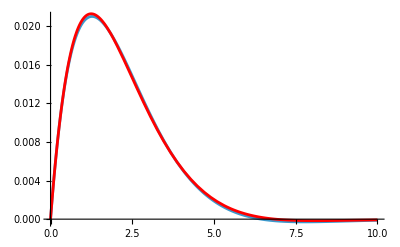

```mathematica
Show[ListLinePlot[q11Data],Plot[nlmq11[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
real11=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq11["ParameterTableEntries"][[2,1]])^2;
```

General::munfl: Exp[-1070.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-844.666] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mreal11=Solve[Mp[[4,4]]-real11==0,mO][[1,1,2]]/.param/.paramScheme
```

2899.37

```mathematica
nlmq21=NonlinearModelFit[q21Data,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf1'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq21["ParameterTable"]
```

General::munfl: Exp[-1316.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1089.3] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.83179 | 0.000157496 | 5281.35 | 0.
xi | 0.829935 | 0.000434186 | 1911.47 | 0.

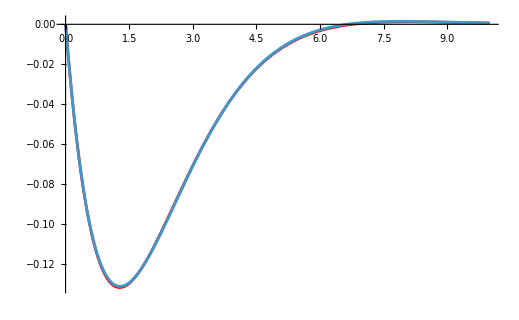

```mathematica
Show[Plot[nlmq21[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q21Data]]
```

```mathematica
real21=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq21["ParameterTableEntries"][[2,1]])^2;
```

General::munfl: Exp[-1316.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1089.3] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mreal21=Solve[Mp[[5,5]]-real21==0,mO][[1,1,2]]/.param/.paramScheme
```

2950.12

```mathematica
nlmq22=NonlinearModelFit[q22Data,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf2'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq22["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.824491 | 0.000564136 | 1461.51 | 1.44512×10^-76
xi | 0.808087 | 0.00147157 | 549.133 | 2.17865×10^-63

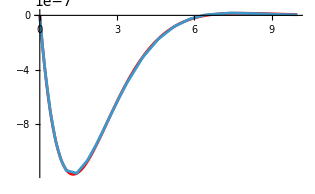

```mathematica
Show[Plot[nlmq22[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q22Data]]
```

```mathematica
real22=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq22["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal22=Solve[Mp[[5,5]]-real22==0,mO][[1,1,2]]/.param/.paramScheme
```

3117.44

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal22}]
```

2924.75

3117.44

#### Nonlinearfit Symbolic Form with noise

```mathematica
w=WhiteNoiseProcess[0.001];
noiseData1=RandomFunction[w,{0,Dimensions[q11Data][[1]]-1}];
noiseData1y=Normal[noiseData1][[1,All,2]];
noiseData2=RandomFunction[w,{0,Dimensions[q22Data][[1]]-1}];
noiseData2y=Normal[noiseData2][[1,All,2]];
```

```mathematica
q11DataNoise=Transpose@{q11Data[[All,1]],q11Data[[All,2]]+noiseData1y};
q21DataNoise=Transpose@{q21Data[[All,1]],q21Data[[All,2]]+noiseData1y};
q12DataNoise=Transpose@{q12Data[[All,1]],q12Data[[All,2]]+noiseData2y};
q22DataNoise=Transpose@{q22Data[[All,1]],q22Data[[All,2]]+noiseData2y};
```

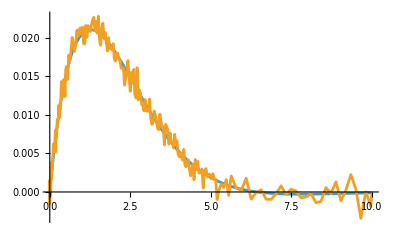

```mathematica
ListLinePlot[{q11Data,q11DataNoise}]
```

```mathematica
nlmq11Symb=NonlinearModelFit[q11DataNoise,q1[t]/.sol11,{{mO,1987}},t]
nlmq11Symb["ParameterTable"]
real11Symbolic=nlmq11Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 758.616 | 53.9354 | 14.0653 | 1.16096×10^-32

758.616

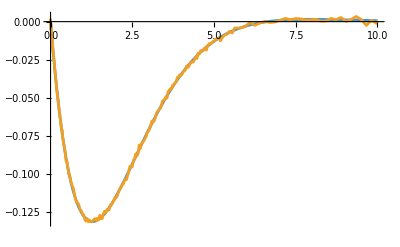

```mathematica
ListLinePlot[{q21Data,q21DataNoise}]
```

```mathematica
0.3*π/180
```

0.00523599

```mathematica
nlmq21Symb=NonlinearModelFit[q21DataNoise,q2[t]/.sol21,{{mO,1987}},t]
nlmq21Symb["ParameterTable"]
real21Symbolic=nlmq21Symb["ParameterTableEntries"][[1,1]]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

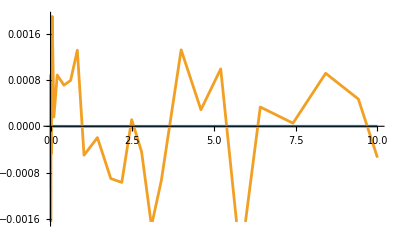

```mathematica
ListLinePlot[{q22Data,q22DataNoise}]
```

```mathematica
nlmq22Symb=NonlinearModelFit[q22DataNoise,q2[t]/.sol22,{{mO,0}},t]
nlmq22Symb["ParameterTable"]
real22Symbolic=nlmq22Symb["ParameterTableEntries"][[1,1]]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {-0.000136798 + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[<<8>>4 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {0.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {-0.000136798 + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[<<8>>4 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {0.}.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«22»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {-0.000136798 + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[<<8>>4 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {0.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {-0.000136798 + (q2[0.] /. {q2[0.] (3124.81 + <<157>> - Divide[<<8>>4 <<2>>, <<1>>]) + <<3>> == 0., <<2>>}), <<32>>} is not a list of real numbers with dimensions {33} at {mO} = {0.}.

Part::partd: Part specification «1» is longer than depth of object.

```mathematica
Mean[{real11Symbolic,real21Symbolic}]
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {q2[0.] (3124.81+60734.5 Cos[«1»]^2+1749.15 Cos[«1»]^2 Cos[«1»]^2+12.5939 Cos[«1»]^2 Cos[«1»]^4+60734.5 Sin[«1»]^2+«74»+«109»)+«2»+(3124.81+30.3672 mO Cos[«1»]^2+0.874576 mO Cos[«1»]^2 Cos[«1»]^2+0.00629695 mO Cos[«1»]^2 Cos[«1»]^4+«9»+0.00629695 mO Cos[q2[«1»]] Sin[q2[«1»]] Sin[«1»]^2 Sin[Times[«2»]]+0.00157424 mO Cos[«1»]^2 Sin[«1»]^2+0.00157424 mO Sin[«1»]^2 Sin[«1»]^2) q2''[0.]==0,«1»,q2'[0]==-«19»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

Part::partd: Part specification «1» is longer than depth of object.

NonlinearModelFit::nrlnum: The function value {<<696110832 bytes>>} is not a list of real numbers with dimensions {226} at {mO} = {1987.}.

General::stop: Further output of NonlinearModelFit::nrlnum will be suppressed during this calculation.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

#### Nonlinear Model Fit with noise

```mathematica
nlmq11=NonlinearModelFit[q11DataNoise,{(pf1'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t]},{{ω,0.8},{xi,0.8}},t];
```

```mathematica
nlmq11["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.851098 | 0.00332016 | 256.342 | 1.63515×10^-278
xi | 0.833607 | 0.00892903 | 93.3593 | 2.57063×10^-181

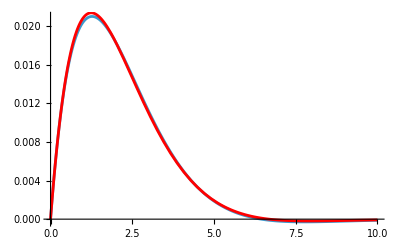

```mathematica
Show[ListLinePlot[q11Data],Plot[nlmq11[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
real11=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq11["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal11=Solve[Mp[[4,4]]-real11==0,mO][[1,1,2]]/.param/.paramScheme
```

2968.46

```mathematica
nlmq21=NonlinearModelFit[q21DataNoise,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf1'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq21["ParameterTable"]
```

General::munfl: Exp[-1031.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-803.656] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.831491 | 0.000564027 | 1474.2 | 0.
xi | 0.831389 | 0.00155738 | 533.837 | 0.

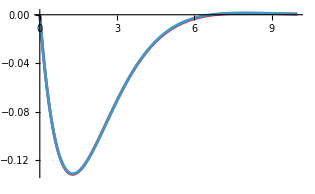

```mathematica
Show[Plot[nlmq21[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q21Data]]
```

```mathematica
real21=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq21["ParameterTableEntries"][[2,1]])^2;
```

General::munfl: Exp[-1031.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-803.656] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
mreal21=Solve[Mp[[5,5]]-real21==0,mO][[1,1,2]]/.param/.paramScheme
```

2939.45

```mathematica
nlmq22=NonlinearModelFit[q22DataNoise,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf2'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[…]

```mathematica
nlmq22["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.919909 | 0.0871446 | -10.5561 | 8.6629×10^-12
xi | 0.713897 | 0.0657264 | 10.8616 | 4.29396×10^-12

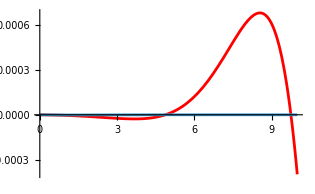

```mathematica
Show[Plot[nlmq22[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q22Data]]
```

```mathematica
real22=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq22["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal22=Solve[Mp[[5,5]]-real22==0,mO][[1,1,2]]/.param/.paramScheme
```

4023.26

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal22}]
```

2953.95

4023.26

#### Parametric Plot Symbolic

Per la simulazion 12, l’approssimazione è troppo simile al valore vero, per cui questo metodo non converge.

```mathematica
{disp11,time11}=FindMinimum[solMotionControl1[[4,2]],{t,1,4}];
{disp21,time21}=FindMaximum[solMotionControl1[[5,2]],{t,1,2}];
{disp12,time12}=FindMaximum[solMotionControl2[[4,2]],{t,1,4}];
{disp22,time22}=FindMaximum[solMotionControl2[[5,2]],{t,1,4}];
```

InterpolatingFunction::dmval: Input value {-0.0397034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00389412} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000665195} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.468085} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.121517} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0397034} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.0397034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00389412} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000665195} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

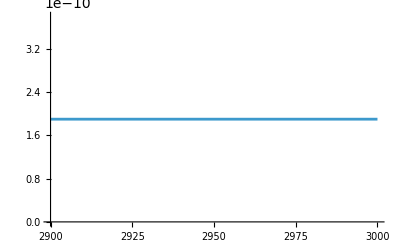

```mathematica
Plot[FullSimplify@(sol22[[1,2]]/.t->time22[[1,2]])-disp22,{mO,2900,3000}]
```

```mathematica
mreal11=FindRoot[FullSimplify@(sol11[[1,2]]/.t->time11[[1,2]])-disp11,{mO,1000,10000}][[1,2]]
mreal21=Re@FindRoot[FullSimplify@(sol21[[1,2]]/.t->time21[[1,2]])-disp21,{mO,2000,4000}][[1,2]]
mreal22=FindRoot[FullSimplify@(sol22[[1,2]]/.t->time22[[1,2]])-disp22,{mO,2900,3000}][[1,2]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1.95129×10^11

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

4000.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

3000.

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal22}]
```

9.75646×10^10

3000.

```mathematica
(1-Mean[{mreal11,mreal21}]/mO/.param)*100
(1-Mean[{mreal22}]/mO/.param)*100
```

-3.25215×10^9

0.

#### Parametric Plot

```mathematica
D[(q0'/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t],t]//Simplify
FullSimplify[D[q0(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(q0'+q0 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t],t]]
```

ⅇ^(-t xi ω) (Cos[t √(1-xi^2) ω]-(xi Sin[t √(1-xi^2) ω])/(√(1-xi^2))) q0'

ⅇ^(-t xi ω) (q0 xi ω Cos[t √(1-xi^2) ω]+Cos[t √(1-xi^2) ω] q0'-(Sin[t √(1-xi^2) ω] (q0 (-1+xi^2) ω+xi q0'))/(√(1-xi^2)))

```mathematica
ωd=Simplify[Sqrt[1-mtest/m]Sqrt[mtest/m]];
β=Simplify[Sqrt[1-mtest/m]/Sqrt[mtest/m]];
```

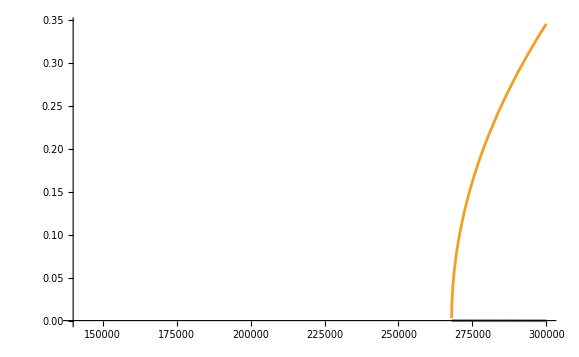

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time11[[1,2]]],β/.mtest->Mpstim[[4,4]]/.param/.paramScheme},{m,140000,300000}]
```

```mathematica
real11=FindRoot[Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time11[[1,2]]]-β/.mtest->Mpstim[[4,4]]/.param/.paramScheme,{m,150000,200000}]
mreal11=Solve[Mp[[4,4]]-real11[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→267961.-2.46261×10^-15 ⅈ}

2000.-2.02715×10^-17 ⅈ

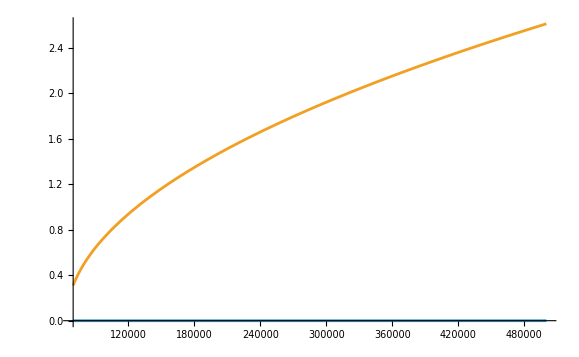

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time21[[1,2]]],β/.mtest->Mpstim[[5,5]]/.param/.paramScheme},{m,70000,500000}]
```

```mathematica
real21=FindRoot[Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time21[[1,2]]]-β/.mtest->Mpstim[[5,5]]/.param/.paramScheme,{m,80000,100000}]
mreal21=Solve[Mp[[5,5]]-real21[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→63865.6-2.79072×10^-13 ⅈ}

2000.-9.18894×10^-15 ⅈ

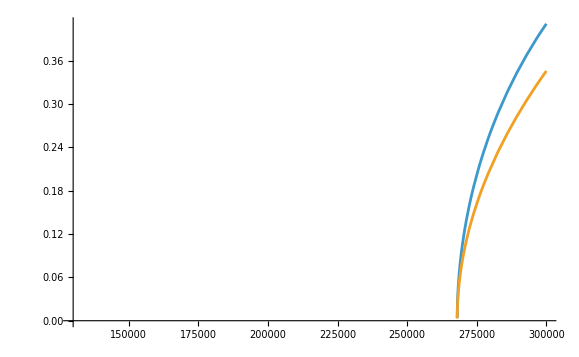

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time12[[1,2]]],β/.mtest->Mpstim[[4,4]]/.param/.paramScheme},{m,130000,300000}]
```

```mathematica
real12=FindRoot[Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time21[[1,2]]]-β/.mtest->Mpstim[[4,4]]/.param/.paramScheme,{m,187000,200000}]
mreal12=Solve[Mp[[4,4]]-real12[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→267961.-8.46668×10^-16 ⅈ}

2000.-6.96953×10^-18 ⅈ

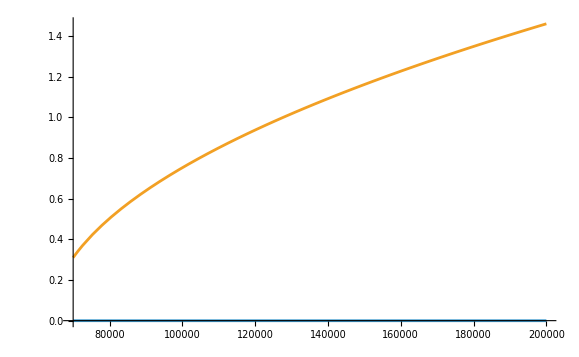

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time22[[1,2]]],β/.mtest->Mpstim[[5,5]]/.param/.paramScheme},{m,70000,200000}]
```

```mathematica
real22=FindRoot[Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time22[[1,2]]]-β/.mtest->Mpstim[[5,5]]/.param/.paramScheme,{m,70000,100000}]
mreal22=Solve[Mp[[5,5]]-real22[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{m→63865.6-2.54259×10^-11 ⅈ}

2000.-8.37194×10^-13 ⅈ

```mathematica
realmass1=Mean[{mreal11,mreal21}]
realmass2=Mean[{mreal12,mreal22}]
```

2000.-4.60461×10^-15 ⅈ

2000.-4.18601×10^-13 ⅈ

```mathematica
(1-Mean[{mreal11,mreal21}]/mO/.param)*100
(1-Mean[{mreal12,mreal22}]/mO/.param)*100
```

33.3333+1.53487×10^-16 ⅈ

33.3333+1.39534×10^-14 ⅈ

## Kinetic Parameters Extraction

```mathematica
initialConditionsSymbolic={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0};
```

Initial object’s velocities without knowing Ω’[t]:

```mathematica
solVel1=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[2]]]==ψf1'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[3]]]==ψf1'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
solVel2=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[2]]]==ψf2'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[3]]]==ψf2'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.0000992037,0.114819,-0.116493},{0.000826697,0.956826,-0.970773}} may contain significant numerical errors.

xO'[t]==0.31251&&yO'[t]==0&&Ω'[t]==812.577

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.0000992037,0.114819,-1.00649×10^-6},{0.000826697,0.956826,-8.3874×10^-6}} may contain significant numerical errors.

xO'[t]==-0.00990321&&yO'[t]==-1.49646&&Ω'[t]==11.4722

Initial object' s velocities knowing Ω'[t] :

```mathematica
solVel1Acc=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf1'[[2]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
solVel2Acc=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf2'[[2]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

xO'[t]==1.01458&&yO'[t]==0

xO'[t]==8.76586×10^-6&&yO'[t]==-1.49646

```mathematica
momentumEq1=Chop@Simplify[M.(p'/.{p'[[1]]->pf1'[[1]],p'[[2]]->pf1'[[2]],p'[[3]]->pf1'[[3]],p'[[4]]->pf1'[[4]],p'[[5]]->pf1'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf1'[[1]],yO'[t]->ψf1'[[2]],Ω'[t]->ψf1'[[3]]})-({xO'[t],yO'[t],Ω'[t]}))/.paramExtraction/.mO->realmass1/.paramScheme/.Ω'[t]->0]
Solve[{momentumEq1[[1]]==0,momentumEq1[[2]]==0},{xO'[t],yO'[t]}][[1]]
```

{2000.35-1971.61 xO'[t],-2000. yO'[t],-22363.9+22042.6 xO'[t],-22363.9+22042.6 xO'[t],-11181.9+11021.3 xO'[t]}

{xO'[t]→1.01458,yO'[t]→0.}

```mathematica
momentumEq2=Chop@Simplify[M.(p'/.{p'[[1]]->pf2'[[1]],p'[[2]]->pf2'[[2]],p'[[3]]->pf2'[[3]],p'[[4]]->pf2'[[4]],p'[[5]]->pf2'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf2'[[1]],yO'[t]->ψf2'[[2]],Ω'[t]->ψf2'[[3]]})-({xO'[t],yO'[t],Ω'[t]}))/.paramExtraction/.mO->realmass2/.paramScheme/.Ω'[t]->0]
sol2=Solve[{momentumEq2[[1]]==0,momentumEq2[[2]]==0},{xO'[t],yO'[t]}][[1]]
```

{0.0172829-1971.61 xO'[t],-2992.91-2000. yO'[t],-0.193222+22042.6 xO'[t],-0.193222+22042.6 xO'[t],-0.0966112+11021.3 xO'[t]}

{xO'[t]→8.76586×10^-6,yO'[t]→-1.49646}